## AES Cryptosystem

### 字节代替

```mathematica
pS={"637c777bf26b6fc53001672bfed7ab76","ca82c97dfa5947f0add4a2af9ca472c0","b7fd9326363ff7cc34a5e5f171d83115","04c723c31896059a071280e2eb27b275","09832c1a1b6e5aa0523bd6b329e32f84","53d100ed20fcb15b6acbbe394a4c58cf","d0efaafb434d338545f9027f503c9fa8","51a3408f929d38f5bcb6da2110fff3d2","cd0c13ec5f974417c4a77e3d645d1973","60814fdc222a908846eeb814de5e0bdb","e0323a0a4906245cc2d3ac629195e479","e7c8376d8dd54ea96c56f4ea657aae08","ba78252e1ca6b4c6e8dd741f4bbd8b8a","703eb5664803f60e613557b986c11d9e","e1f8981169d98e949b1e87e9ce5528df","8ca1890dbfe6426841992d0fb054bb16"};
pInvS={"52096ad53036a538bf40a39e81f3d7fb","7ce339829b2fff87348e4344c4dee9cb","547b9432a6c2233dee4c950b42fac34e","082ea16628d924b2765ba2496d8bd125","72f8f66486689816d4a45ccc5d65b692","6c704850fdedb9da5e154657a78d9d84","90d8ab008cbcd30af7e45805b8b34506","d02c1e8fca3f0f02c1afbd0301138a6b","3a9111414f67dcea97f2cfcef0b4e673","96ac7422e7ad3585e2f937e81c75df6e","47f11a711d29c5896fb7620eaa18be1b","fc563e4bc6d279209adbc0fe78cd5af4","1fdda8338807c731b11210592780ec5f","60517fa919b54a0d2de57a9f93c99cef","a0e03b4dae2af5b0c8ebbb3c83539961","172b047eba77d626e169146355210c7d"};
rpInvS=ToUpperCase[(StringJoin[#]&/@Partition[StringSplit[Characters[#]],2])&/@pInvS];
S[str__]:=StringJoin[ToString/@(First@Position[rpInvS,ToUpperCase@str]-1/.{10->"A",11->"B",12->"C",13->"D",14->"E",15->"F"})];
rS=ToUpperCase[(StringJoin[#]&/@Partition[StringSplit[Characters[#]],2])&/@pS];
InvS[str__]:=StringJoin[ToString/@(First@Position[rS,ToUpperCase@str]-1/.{10->"A",11->"B",12->"C",13->"D",14->"E",15->"F"})];
```

```mathematica
S["00"]
```

63

```mathematica
InvS["63"]
```

00

### 行移位

```mathematica
t={{0,1,2,3},{1,2,3,4},{2,3,4,5},{3,4,5,6}};
```

```mathematica
RotateLeft[S[[#]],#-1]&/@Range[1,Length[t]]
```

{{0,1,2,3},{2,3,4,1},{4,5,2,3},{6,3,4,5}}

## RSA

```mathematica
p=RandomPrime[{10^15,10^20}];
q=RandomPrime[{10^15,10^20}];
n=p q;
pn=(p-1)(q-1);
e=748327;
If[GCD[e,pn]==1,
d=PowerMod[e,-1,pn];
m=1084005572813748151399292456053001553605;
c=PowerMod[m,e,n];
Print[c];
de=PowerMod[c,d,n]]
```

3307776670135161359227678460173772257622

1084005572813748151399292456053001553605

## ECC

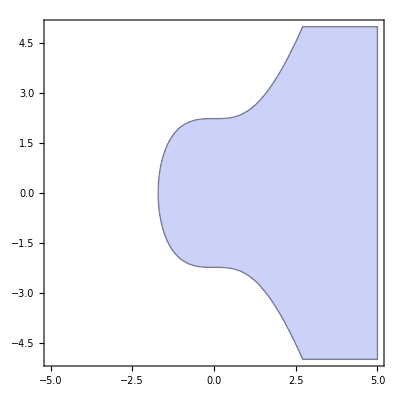

```mathematica
RegionPlot[y^2≤x^3+5,{x,-5,5},{y,-5,5}]
```